Louf et al. model Coexistence Region in Parameter Space

```mathematica
texMathStyle={FontFamily->"CMU Serif",FontSize->7*1.5};
texTextStyle = {FontFamily-> "Latin Modern Sans", FontSize->7*1.5} ;
```

Master equations in terms of parameter r (divide original ones by c(1-\mu) and arbitrarily rescale time by this factor)

```mathematica
xeq = r*(1-x-y)*s*(x+q*(1-x-y))-x*(1-s)*(y+(1-q)*(1-x-y)); 
yeq = r*(1-x-y)*(1-s)*(y+(1-q)*(1-x-y))-y*s*(x+q*(1-x-y));
```

Calculation of the eigenvalues

```mathematica
genericEigen = Eigenvalues[{
{D[xeq, x], D[xeq, y]},
{D[yeq, x], D[yeq, y]}
}];
```

Finding the fixed points of the model

```mathematica
sol = Solve[{xeq==0, yeq==0}, {x, y},NonNegativeReals];
```

Solution that gives coexistance checked to be #5. Simplify the solution assuming that the parameters are in their range of definition

```mathematica
generalCoexSol = Assuming[r>0 && q<1 && s<1 && s>0 && q>0 && r<1, Simplify@sol[[5]]];
```

Obtention of the conditions on parameters that make such coexisting solution exist

```mathematica
boolCoex = FirstCase[x/.generalCoexSol,ConditionalExpression[_,c_]:>c,Missing[],{0,-1}];
```

Calculation of real part of eigenvalues (useful in the future to check stability)

```mathematica
eigenCoex = Re@Normal@(genericEigen/.generalCoexSol);
```

Eigenvalues, range of existence in parameter space and x* and y* for the coexisting solution for the values of s in which we are interested

```mathematica
symPrestEigen = eigenCoex/.{s->0.5};
symPrestboolCoex = boolCoex/.{s->0.5};
symPrestSolCoex = Normal@generalCoexSol/.{s->0.5};
asymPrestEigenDown = eigenCoex/.{s->0.3};
asymPrestboolCoexDown = boolCoex/.{s->0.3};
asymPrestSolCoexDown = Normal@generalCoexSol/.{s->0.3};
asymPrestEigenMax = eigenCoex/.{s->0.4};
asymPrestboolCoexMax = boolCoex/.{s->0.4};
asymPrestSolCoexMax = Normal@generalCoexSol/.{s->0.4};
```

Representation of the coexisting regions in parameter space for the desired values of s. For each case conditions to determine the range are as follows: 1st and 2nd eigenvalues are negative, necessary for stability. 3rd conditions of parameters for that solution to exist. 4th and 5th x* and y* are less than 1 so they have physical meaning.

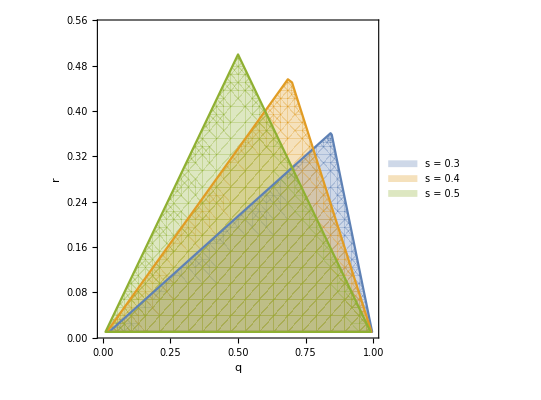

```mathematica
coex2DRegionPlotRedux = RegionPlot[{

asymPrestEigenDown[[1]] <0 && asymPrestEigenDown[[2]]<0 && asymPrestboolCoexDown && (x/.asymPrestSolCoexDown) < 1 && (y/.asymPrestSolCoexDown) < 1, 
asymPrestEigenMax[[1]] <0 && asymPrestEigenMax[[2]]<0 && asymPrestboolCoexMax && (x/.asymPrestSolCoexMax) < 1 && (y/.asymPrestSolCoexMax) < 1, 
symPrestEigen[[1]] <0 && symPrestEigen[[2]]<0 && symPrestboolCoex && (x/.symPrestSolCoex) < 1 && (y/.symPrestSolCoex) < 1}, 
{q, 0,1},{r, 0.01, 0.55},  FrameLabel->{q, r},AxesLabel->Automatic, Frame->{{True,False},{True,False}},
PlotLegends->Placed[SwatchLegend[{"s = 0.3", "s = 0.4", "s = 0.5"}, LabelStyle-> texMathStyle], {Scaled[{0.95,0.8}], {1, 1}}],
BaseStyle->texMathStyle]
```